# Single triangular plaquette pseudo-spin dynamics

```mathematica
{z1, z2, z3} = KroneckerProduct@@@Permutations[{PauliMatrix[3], PauliMatrix[0], PauliMatrix[0]}];
{x1, x2,x3} = KroneckerProduct@@@Permutations[{PauliMatrix[1], PauliMatrix[0], PauliMatrix[0]}];
```

```mathematica
formHam[j_,gam_]:=j (z1.z2 + z1.z3 + z2.z3) - gam(x1 + x2 + x3);
```

```mathematica
formHam[1, 0.1]
```

{{3.,-0.1,-0.1,0.,-0.1,0.,0.,0.},{-0.1,-1.,0.,-0.1,0.,-0.1,0.,0.},{-0.1,0.,-1.,-0.1,0.,0.,-0.1,0.},{0.,-0.1,-0.1,-1.,0.,0.,0.,-0.1},{-0.1,0.,0.,0.,-1.,-0.1,-0.1,0.},{0.,-0.1,0.,0.,-0.1,-1.,0.,-0.1},{0.,0.,-0.1,0.,-0.1,0.,-1.,-0.1},{0.,0.,0.,-0.1,0.,-0.1,-0.1,3.}}

```mathematica
formVec[stringState_]:=Module[{up, down, right, left, mapping, vecList,vec},
up = {1, 0};
down = {0, 1};
right = {1, 1}/Sqrt[2];
left = {1, -1}/Sqrt[2];
mapping = <|"u"->up,"d"->down,"r"->right,"l"->left |>;
vecList =Lookup[Characters[stringState]]@mapping;
vec = KroneckerProduct@@vecList//Flatten;

Return[vec];
]
compComm[a_,b_]:=a.b-b.a
```

```mathematica
h = formHam[1, 0.1];
ut = MatrixExp[-ⅈ h t];
hp = h + z1;
hm = h - z1;
utp = MatrixExp[-ⅈ hp t];
utm = MatrixExp[-ⅈ hm t];
psiOp = (z1 + z2*Exp[2π ⅈ /3]+z3*Exp[4π ⅈ/3])/Sqrt[3];
computePsi[state_]:=ConjugateTranspose[state].psiOp.state;
```

```mathematica
phi0 = formVec["duu"];
T = 100;
dt = 1/10;
eps = 10^-5;

vect = ut.phi0;
vecDiscT = Table[vect/.{t->tv}, {tv, 0, T, dt}];
pseudoSpins = computePsi[#]&/@vecDiscT;
pSpinPoints = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpins;
z1ExpVals =Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscT;
z2ExpVals =Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscT;
z3ExpVals =Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscT;

vectp = utp.phi0;
vecDiscTp = Table[vectp/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsp = computePsi[#]&/@vecDiscTp;
pSpinPointsp = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpinsp;
z1ExpValsp = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTp;
z2ExpValsp = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTp;
z3ExpValsp = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTp;

vectm = utm.phi0;
vecDiscTm = Table[vectm/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsm = computePsi[#]&/@vecDiscTm;
pSpinPointsm = Chop[{Re[#],Im[#]},eps]&/@pseudoSpinsm;
z1ExpValsm = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTm;
z2ExpValsm = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTm;
z3ExpValsm = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTm;
```

```mathematica
Animate[ListPlot[{{pSpinPoints[[i]]}, {pSpinPointsp[[i]]}, {pSpinPointsm[[i]]}}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H", "H + Z_1", "H - Z_1"}], {i, 1, Length[pSpinPoints], 1}]
```

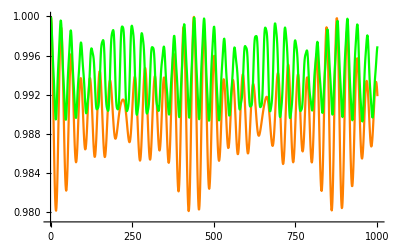

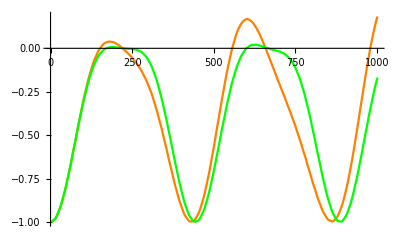

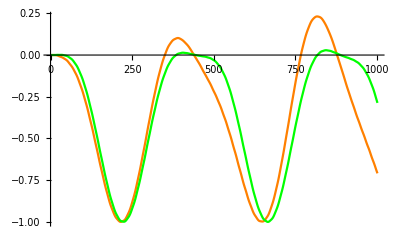

```mathematica
ListPlot[{z1ExpValsp, z1ExpValsm},Joined->True, PlotStyle->{Orange, Green}]
ListPlot[{z2ExpValsp, z2ExpValsm},Joined->True, PlotStyle->{Orange, Green}]
ListPlot[{z3ExpValsp, z3ExpValsm},Joined->True, PlotStyle->{Orange, Green}]
```

```mathematica
(z1ExpVals[[1]]-z2ExpVals[[1]]) /Sqrt[3]
```

-1.1547

```mathematica
Exp[2π ⅈ / 3]+Exp[4π ⅈ / 3]//N
```

-1.+0. ⅈ

```mathematica
(z1ExpVals[[1]]+z2ExpVals[[2]]*Exp[2π ⅈ / 3]+z3ExpVals[[3]]*Exp[4π ⅈ / 3]) / Sqrt[3]
```

-1.15441+0.000299946 ⅈ

```mathematica
z1t[t_]=ConjugateTranspose[ut].z1.ut;
```

```mathematica
Chop[z1t[0], 10^-5]==z1
```

True

```mathematica
psit[t_]=ConjugateTranspose[ut].psiOp.ut;
```

```mathematica
phi0.Chop[psit[0.2], 10^-5].phi0
```

0.865351-0.49961 ⅈ

```mathematica
Chop[psit[0], 10^-5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.57735+1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.57735-1. ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.1547 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.1547 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.57735+1. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.57735-1. ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Chop[psit[0.001], 10^-5][[]]
```

(0 | 0.000100115-0.0000575349 ⅈ | -0.0000998843-0.0000579349 ⅈ | 0 | 0.+0.00011547 ⅈ | 0 | 0 | 0
-0.0000998843+0.0000579349 ⅈ | 0.57735+1. ⅈ | 0 | -0.0001-0.000057735 ⅈ | 0 | 0.+0.00011547 ⅈ | 0 | 0
0.000100115+0.0000575349 ⅈ | 0 | 0.57735-1. ⅈ | 0.0001-0.000057735 ⅈ | 0 | 0 | 0.+0.00011547 ⅈ | 0
0 | 0.0001+0.000057735 ⅈ | -0.0001+0.000057735 ⅈ | 1.1547 | 0 | 0 | 0 | 0.+0.00011547 ⅈ
0.-0.00011547 ⅈ | 0 | 0 | 0 | -1.1547 | 0.0001-0.000057735 ⅈ | -0.0001-0.000057735 ⅈ | 0
0 | 0.-0.00011547 ⅈ | 0 | 0 | -0.0001+0.000057735 ⅈ | -0.57735+1. ⅈ | 0 | -0.000100115-0.0000575349 ⅈ
0 | 0 | 0.-0.00011547 ⅈ | 0 | 0.0001+0.000057735 ⅈ | 0 | -0.57735-1. ⅈ | 0.0000998843-0.0000579349 ⅈ
0 | 0 | 0 | 0.-0.00011547 ⅈ | 0 | 0.0000998843+0.0000579349 ⅈ | -0.000100115+0.0000575349 ⅈ | 0)

```mathematica
Chop[psit[0][[5, 5]], 10^-5]
```

-1.1547

```mathematica
MatrixPartialTrace[z1, {2,3},2]
```

{{4,0},{0,-4}}

```mathematica
MatrixPartialTrace[z1, Except[{1}],2]
```

{{4,0},{0,-4}}

```mathematica
test = KroneckerProduct[PauliMatrix[1], PauliMatrix[0]];
MatrixPartialTrace[test, Except[{1}],2]
```

{{0,2},{2,0}}

```mathematica
test
```

{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}

```mathematica
vect = ut.phi0;
```

```mathematica
ρ = KroneckerProduct[vect, ConjugateTranspose[vect]];
ρ1 = MatrixPartialTrace[ρ, Except[{1}], 2];
ρ2 = MatrixPartialTrace[ρ, Except[{2}], 2];
ρ3 = MatrixPartialTrace[ρ, Except[{3}], 2];
```

```mathematica
Tr[(ρ/.{t->T}).z1]
```

0.399265-1.04083×10^-17 ⅈ

```mathematica
Tr[(ρ1/.{t->T}).PauliMatrix[3]]
```

0.399265-1.04083×10^-17 ⅈ

```mathematica
f1 = Tr[ρ1.PauliMatrix[3]];
f2= Tr[ρ2.PauliMatrix[3]];
f3 = Tr[ρ3.PauliMatrix[3]];
```

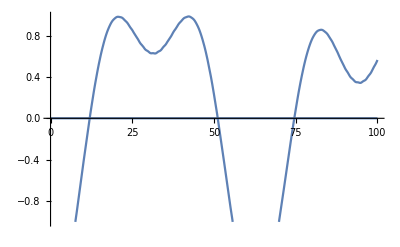

```mathematica
Plot[{Re[#],Im[#]}&/@(f1+f2*Exp[2π ⅈ/3]+f3*Exp[4π ⅈ/3])/.{t->tp}, {tp, 0, 100}]
```

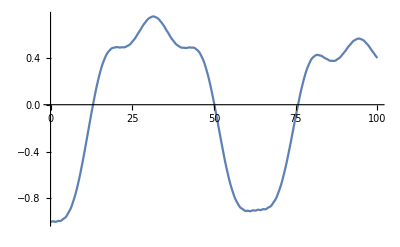

```mathematica
Plot[Re[f1]/.{t->tp}, {tp, 0, 100}]
```

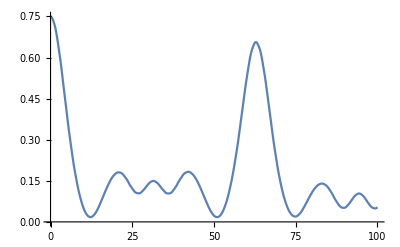

```mathematica
Plot[(f1/2/.{t->tp})^2+(f2/2/.{t->tp})^2+(f3/2/.{t->tp})^2, {tp, 0, 100}]
```

```mathematica
{v1x, v1y, v1z} = {Tr[ρ1.PauliMatrix[1]], Tr[ρ1.PauliMatrix[2]], Tr[ρ1.PauliMatrix[3]]};
coherences1 = Table[(v1x/.{t->tv}//Re)^2+(v1y/.{t->tv}//Re)^2+(v1z/.{t->tv}//Re)^2, {tv, 0, T, dt}];
{v2x, v2y, v2z} = {Tr[ρ2.PauliMatrix[1]], Tr[ρ2.PauliMatrix[2]], Tr[ρ2.PauliMatrix[3]]};
coherences2 = Table[(v2x/.{t->tv}//Re)^2+(v2y/.{t->tv}//Re)^2+(v2z/.{t->tv}//Re)^2, {tv, 0, T, dt}];
{v3x, v3y, v3z} = {Tr[ρ3.PauliMatrix[1]], Tr[ρ3.PauliMatrix[2]], Tr[ρ3.PauliMatrix[3]]};
coherences3 = Table[(v3x/.{t->tv}//Re)^2+(v3y/.{t->tv}//Re)^2+(v3z/.{t->tv}//Re)^2, {tv, 0, T, dt}];
```

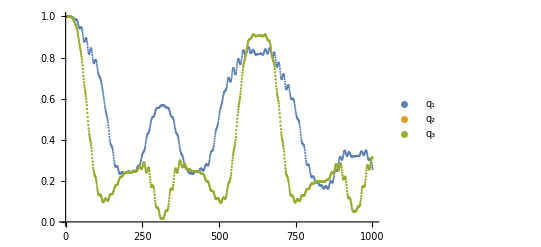

```mathematica
ListPlot[{coherences1, coherences2, coherences3}, PlotLegends->{"q_1", "q_2", "q_3"}]
```

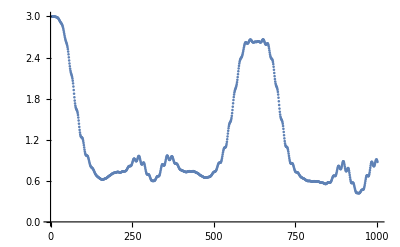

```mathematica
ListPlot[coherences1+coherences2+coherences3]
```

```mathematica
phi0 = formVec["urr"];
T = 100;
dt = 1/10;
eps = 10^-5;

vect = ut.phi0;
vecDiscT = Table[vect/.{t->tv}, {tv, 0, T, dt}];
pseudoSpins = computePsi[#]&/@vecDiscT;
pSpinPoints = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpins;
z1ExpVals =Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscT;
z2ExpVals =Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscT;
z3ExpVals =Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscT;

vectp = utp.phi0;
vecDiscTp = Table[vectp/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsp = computePsi[#]&/@vecDiscTp;
pSpinPointsp = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpinsp;
z1ExpValsp = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTp;
z2ExpValsp = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTp;
z3ExpValsp = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTp;

vectm = utm.phi0;
vecDiscTm = Table[vectm/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsm = computePsi[#]&/@vecDiscTm;
pSpinPointsm = Chop[{Re[#],Im[#]},eps]&/@pseudoSpinsm;
z1ExpValsm = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTm;
z2ExpValsm = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTm;
z3ExpValsm = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTm;
```

```mathematica
Animate[ListPlot[{{pSpinPoints[[i]]}, {pSpinPointsp[[i]]}, {pSpinPointsm[[i]]}}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H", "H + Z_1", "H - Z_1"}], {i, 1, Length[pSpinPoints], 1}]
```

```mathematica
formVec["urr"]
```

{1/2,1/2,1/2,1/2,0,0,0,0}

```mathematica
swap12 = KroneckerProduct[{{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}, PauliMatrix[0]];
```

```mathematica
swap12H = ⅈ MatrixLog[swap12];
```

```mathematica
MatrixExp[-ⅈ (100*swapH+z1)(1/100)].formVec["urr"]//N
```

{0.499975-0.00499992 ⅈ,0.499975-0.00499992 ⅈ,0.00318303-0.0000159153 ⅈ,0.00318303-0.0000159153 ⅈ,0.49999-1.61173×10^-17 ⅈ,0.49999-1.61173×10^-17 ⅈ,0.,0.}

```mathematica
formVec["rur"]//N
```

{0.5,0.5,0.,0.,0.5,0.5,0.,0.}

```mathematica
phi0 = formVec["urr"];
T = 1/10;
dt = 1/100;
eps = 10^-5;

vect = ut.phi0;
vecDiscT = Table[vect/.{t->tv}, {tv, 0, T, dt}];
pseudoSpins = computePsi[#]&/@vecDiscT;
pSpinPoints = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpins;
z1ExpVals =Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscT;
z2ExpVals =Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscT;
z3ExpVals =Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscT;

uswap12t = MatrixExp[-ⅈ (1/T*swap12H+h)t];
vectp = uswap12t.phi0;
vecDiscTp = Table[vectp/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsp = computePsi[#]&/@vecDiscTp;
pSpinPointsp = Chop[{Re[#],Im[#]}, eps]&/@pseudoSpinsp;
z1ExpValsp = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTp;
z2ExpValsp = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTp;
z3ExpValsp = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTp;

uswap12tm = MatrixExp[-ⅈ (-1/T*swap12H+h)t];
vectm = uswap12tm.phi0;
vecDiscTm = Table[vectm/.{t->tv}, {tv, 0, T, dt}];
pseudoSpinsm = computePsi[#]&/@vecDiscTm;
pSpinPointsm = Chop[{Re[#],Im[#]},eps]&/@pseudoSpinsm;
z1ExpValsm = Chop[Re[ConjugateTranspose[#].z1.#],eps]&/@vecDiscTm;
z2ExpValsm = Chop[Re[ConjugateTranspose[#].z2.#],eps]&/@vecDiscTm;
z3ExpValsm = Chop[Re[ConjugateTranspose[#].z3.#],eps]&/@vecDiscTm;
```

```mathematica
Animate[ListPlot[{{pSpinPoints[[i]]}, {pSpinPointsp[[i]]}, {pSpinPointsm[[i]]}}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H", "H + Z_1", "H - Z_1"}], {i, 1, Length[pSpinPoints], 1}]
```